# Práctica 3

Ejercicio1:

S1)

```mathematica
b={0.1,0.1,-1,0.3}
a=Transpose[RowReduce[{{1,1,2,3},{1,1,1,3},{0,1.2,2.3,3.4}}]]
```

{0.1,0.1,-1,0.3}

```mathematica
Solve[Transpose[a].a.{x,y,z}==Transpose[a].b,{x,y,z}]
```

{{x→0.1,y→0.1,z→-1.}}

```mathematica
c=a.{0.1,0.1,-1}
```

{0.1,0.1,-1.,0.3}

```mathematica
(b-c).Transpose[a][[1]]
(b-c).Transpose[a][[2]]
(b-c).Transpose[a][[3]]
```

-9.25186×10^-18

-1.57282×10^-16

0.

S2)

```mathematica
Solve[{x-y==0,2x+4.2y-1==0},{x,y}]
```

{{x→0.16129,y→0.16129}}

```mathematica
a=Transpose[{{-3.7,2,1,0},{0.16129,0.16129,0,1}}]
```

{{-3.7,0.16129},{2,0.16129},{1,0},{0,1}}

```mathematica
Solve[Transpose[a].a.{x,y}==Transpose[a].b,{x,y}]
```

{{x→-0.0581895,y→0.30066}}

```mathematica
c=a.{-0.0581895,0.30066}
```

{0.263795,-0.0678855,-0.0581895,0.30066}

```mathematica
(b-c).Transpose[a][[1]]
(b-c).Transpose[a][[2]]
```

6.2238×10^-7

-1.71126×10^-7

Ejercicio 2:

```mathematica
b={2,0,3.2,Pi/9,4,4}
```

{2,0,3.2,π/9,4,4}

```mathematica
a=Transpose[{{1,1,1,1,1,1},{1,0,-1.1,2,0,-19/2}}]
```

{{1,1},{1,0},{1,-1.1},{1,2},{1,0},{1,-19/2}}

```mathematica
c=Transpose[{{1,1,1,1,1,1},{1,0,-1.1,2,0,-19/2},{1,0,(-1.1)^2,4,0,(-19/2)^2}}]
```

{{1,1,1},{1,0,0},{1,-1.1,1.21},{1,2,4},{1,0,0},{1,-19/2,361/4}}

```mathematica
Solve[Transpose[a].a.{n,m}==Transpose[a].b,{n,m}]
```

{{n→1.94222,m→-0.24944}}

```mathematica
Solve[Transpose[c].c.{a0,a1,a2}==Transpose[c].b,{a0,a1,a2}]
```

{{a0→2.26997,a1→-0.752,a2→-0.0599829}}

```mathematica
r[x_]:=-0.24944x+1.94222
```

```mathematica
f[x_]:=-0.0599829x^2-0.752x+2.26997
```

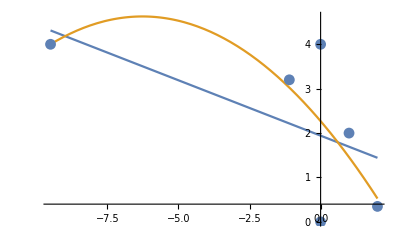

```mathematica
Show[Plot[{r[x],f[x]},{x,-19/2,2},PlotRange->All],ListPlot[{{1,2},{0,0},{-1.1,3.2},{2,Pi/9},{0,4},{-19/2,4}},PlotRange->All]]
```

Ejercicio 3:

```mathematica
f[x_]:=(x-2Pi)^2
```

```mathematica
Id[x_]:=x
Cos2[x_]:=Cos[2x]
Uno[x_]:=1
```

```mathematica
B={Uno,Id,Sin,Cos2,Exp}
```

{Uno,Id,Sin,Cos2,Exp}

```mathematica
productoEscalar[f_,g_]:=Integrate[f[x]*g[x],{x,0,2Pi}]
```

```mathematica
A=Table[productoEscalar[B[[i]],B[[j]]],{i,5},{j,5}]
b=Table[productoEscalar[B[[i]],f],{i,5}]
```

{{2 π,2 π^2,0,0,-1+ⅇ^(2 π)},{2 π^2,(8 π^3)/3,-2 π,0,1+ⅇ^(2 π) (-1+2 π)},{0,-2 π,π,0,-ⅇ^π Sinh[π]},{0,0,0,π,1/5 (-1+ⅇ^(2 π))},{-1+ⅇ^(2 π),1+ⅇ^(2 π) (-1+2 π),-ⅇ^π Sinh[π],1/5 (-1+ⅇ^(2 π)),1/2 (-1+ⅇ^(4 π))}}

{(8 π^3)/3,(4 π^4)/3,4 π^2,π,2 (-1+ⅇ^(2 π)-2 π-2 π^2)}

```mathematica
MatrixForm[A]
MatrixForm[b]
```

(2 π | 2 π^2 | 0 | 0 | -1+ⅇ^(2 π)
2 π^2 | (8 π^3)/3 | -2 π | 0 | 1+ⅇ^(2 π) (-1+2 π)
0 | -2 π | π | 0 | -ⅇ^π Sinh[π]
0 | 0 | 0 | π | 1/5 (-1+ⅇ^(2 π))
-1+ⅇ^(2 π) | 1+ⅇ^(2 π) (-1+2 π) | -ⅇ^π Sinh[π] | 1/5 (-1+ⅇ^(2 π)) | 1/2 (-1+ⅇ^(4 π)))

((8 π^3)/3
(4 π^4)/3
4 π^2
π
2 (-1+ⅇ^(2 π)-2 π-2 π^2))

```mathematica
N[LinearSolve[A,b]]
```

{39.8172,-9.70272,-3.01477,-0.529719,0.0449563}

```mathematica
f1[x_]:=39.8172B[[1]][x]-9.70272B[[2]][x]-3.01477B[[3]][x]-0.529719B[[4]][x]+0.0449563B[[5]][x]
```

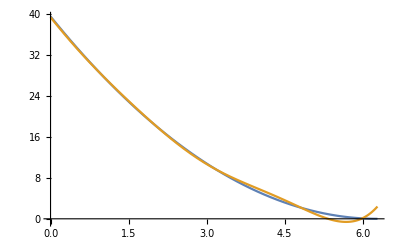

```mathematica
Plot[{f[x],f1[x]},{x,0,2Pi},PlotRange->All]
```

Ejercicio 4

```mathematica
p[j_]:=Cos[j]-1/6Sqrt[j]
```

```mathematica
datos=Table[{j/10,N[p[j/10]]},{j,0,10}];
```

```mathematica
baseLagrange[nodos_]:=Block[{n=Length[nodos],l=Table[0,{k,Length[nodos]}],i,x},For[i=1,i≤n,i++,l[[i]]=Product[If[j≠i,(x-nodos[[j]])/(nodos[[i]]-nodos[[j]]),1],{j,n}]];l]
```

```mathematica
Bl=baseLagrange[Transpose[datos][[1]]];
```

```mathematica
q[x_]=Collect[Sum[datos[[i,2]]*Bl[[i]],{i,Length[Bl]}],x]
```

1.-0.996566 x+7.53145 x^2-47.9359 x^3+186.392 x^4-480.103 x^5+827.079 x^6-941.83 x^7+680.054 x^8-281.859 x^9+51.0416 x^10

```mathematica
f[x_]:=Cos[x]-1/6Sqrt[x]
```

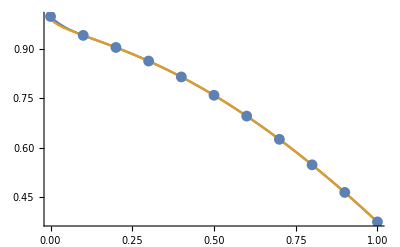

```mathematica
Show[Plot[{q[x],f[x]},{x,0,1},PlotRange->All],ListPlot[Table[{x/10,p[x/10]},{x,0,10}],PlotRange->All]]
```

Ejercicio 5:

```mathematica
nodos=Table[j/10,{j,0,10}];
```

```mathematica
f[x_]:=Cos[x]-1/6Sqrt[x]
```

```mathematica
baseNewton[nodos_]:=Block[{n=Length[nodos],w=Table[0,{k,Length[nodos]}],i},For[ i=1,i≤n,i++,w[[i]]=Product[x-nodos[[j]],{j,i-1}]];w]
```

```mathematica
difDiv[nodos_,f_]:=Block[{n=Length[nodos],dd=Table[0,{i,Length[nodos]},{j,Length[nodos]}],valores=Table[f[nodos[[j]]],{j,Length[nodos]}],i,j},For[i=1,i≤n,i++,dd[[i,1]]=valores[[i]]];For[i=2,i≤n,i++,For[j=2,j≤i,j++,dd[[i,j]]=(dd[[i,j-1]]-dd[[i-1,j-1]])/(nodos[[i]]-nodos[[i-j+1]])]];dd]
```

```mathematica
dd=N[difDiv[nodos,f]];
```

```mathematica
MatrixForm[N[dd]]
```

(1. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0.9423 | -0.577005 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0.905531 | -0.367686 | 1.0466 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0.864049 | -0.414816 | -0.235651 | -4.27415 | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0.815652 | -0.483977 | -0.345804 | -0.367175 | 9.76745 | 0. | 0. | 0. | 0. | 0. | 0.
0.759731 | -0.559203 | -0.376132 | -0.101096 | 0.665199 | -18.2045 | 0. | 0. | 0. | 0. | 0.
0.696236 | -0.634953 | -0.378748 | -0.00871754 | 0.230945 | -0.868507 | 28.8933 | 0. | 0. | 0. | 0.
0.625399 | -0.708373 | -0.367103 | 0.038816 | 0.118834 | -0.224223 | 1.07381 | -39.7422 | 0. | 0. | 0.
0.547636 | -0.777633 | -0.346301 | 0.0693401 | 0.0763104 | -0.0850469 | 0.231961 | -1.20264 | 48.1744 | 0. | 0.
0.463496 | -0.841394 | -0.318804 | 0.0916552 | 0.0557877 | -0.0410452 | 0.0733361 | -0.226606 | 1.22004 | -52.1715 | 0.
0.373636 | -0.898604 | -0.286051 | 0.109178 | 0.0438063 | -0.0239629 | 0.0284706 | -0.0640936 | 0.203141 | -1.12989 | 51.0416)

```mathematica
Bw=baseNewton[nodos];
```

```mathematica
q[x_]:=Collect[Sum[dd[[i,i]]*Bw[[i]],{i,Length[Bw]}],x]
```

```mathematica
Simplify[q[x]]
```

1.-0.996566 x+7.53145 x^2-47.9359 x^3+186.392 x^4-480.103 x^5+827.079 x^6-941.83 x^7+680.054 x^8-281.859 x^9+51.0416 x^10

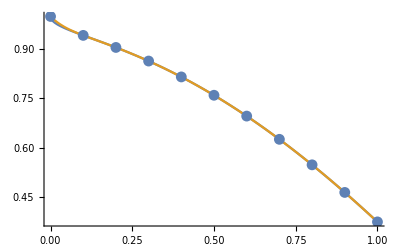

```mathematica
Show[Plot[{f[x],q[x]},{x,0,1},PlotRange->All],ListPlot[Table[{nodos[[i]],f[nodos[[i]]]},{i,Length[nodos]}],PlotRange->All]]
```

Ejercicio 6:

```mathematica
f[x_]:=10.03Cos[2x/Pi]
```

```mathematica
nodos=Table[1-2j/21,{j,0,21}];
```

```mathematica
datos=Table[f[nodos[[j]]],{j,1,22}];
```

```mathematica
perturbados=Table[f[nodos[[j]]+(-1)^j*10^(-3)],{j,1,22}];
```

```mathematica
diferencias=Abs[datos-perturbados];
difMax=diferencias[[1]];
For[i=1,i≤  Length[diferencias],i++,If[diferencias[[i]]>difMax,difMax=diferencias[[i]]]]
```

```mathematica
difMax
```

0.0037943

```mathematica
BL[i_,x_]:=Product[If[j≠i,(x-nodos[[j]])/(nodos[[i]]-nodos[[j]]),1],{j,1,Length[nodos]}]
```

```mathematica
p1[x_]:=Collect[Sum[BL[i,x]*datos[[i]],{i,Length[nodos]}],x]
```

```mathematica
p2[x_]:=Collect[Sum[BL[i,x]*perturbados[[i]],{i,Length[nodos]}],x]
```

```mathematica
diff[x_]:=Abs[p1[x]-p2[x]]
```

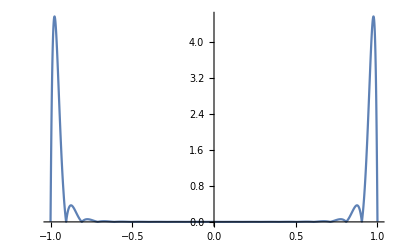

```mathematica
Plot[{diff[x]},{x,nodos[[1]],nodos[[Length[nodos]]]},PlotRange->All]
```

```mathematica
FindMaximum[{diff[x],-1≤x≤1},{x,0.95}]
```

{4.56609,{x→0.975653}}

```mathematica
lambdaN[x_]:=Sum[Abs[BL[i,x]],{i,1,Length[nodos]}]
```

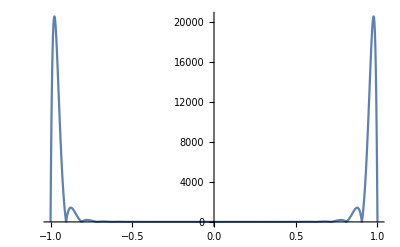

```mathematica
Plot[lambdaN[x],{x,-1,1},PlotRange->All]
```

```mathematica
FindMaximum[{lambdaN[x],-1≤x≤1},{x,0.95}]
```

{20576.3,{x→0.97635}}

```mathematica
(* cteLesbesgue = 20576.3, Mal condicionamiento *)
```

```mathematica
cheb=N[Table[Cos[(1+2i)Pi/44],{i,0,21}]];
```

```mathematica
BL[i_,x_]:=Product[If[j≠i,(x-cheb[[j]])/(cheb[[i]]-cheb[[j]]),1],{j,1,Length[cheb]}]
```

```mathematica
q[x_]:=Collect[Sum[BL[i,x]*f[cheb[[i]]],{i,Length[cheb]}],x]
```

```mathematica
lambdaN[x_]:=Sum[Abs[BL[i,x]],{i,1,Length[cheb]}]
```

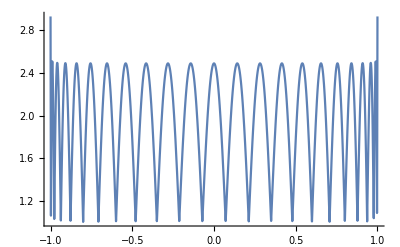

```mathematica
Plot[lambdaN[x],{x,-1,1}]
```

```mathematica
FindMaximum[{lambdaN[x],-1≤x≤1},{x,1}]
```

{2.93043,{x→1.}}

```mathematica
(* cteLesbesgue = 2.9303, Buen condicionamiento *)
```

Ejercicio 7:

```mathematica
nodos=Table[i,{i,1,5}];
y=Table[Log[nodos[[i]]],{i,1,5}];
d=Table[i/2.36,{i,1,5}];
n=Length[nodos];
```

```mathematica
BL[i_,x_]:=Product[If[j≠i,(x-nodos[[j]])/(nodos[[i]]-nodos[[j]]),1],{j,1,Length[nodos]}]
```

```mathematica
H2[i_,x_]:=(1-2(x-nodos[[i]])*D[BL[i,t],{t}]/.t->nodos[[i]])*BL[i,x]^2
H1[i_,x_]:=(x-nodos[[i]])*BL[i,x]^2
```

```mathematica
p[x_]:=Sum[y[[i]]*H2[i,x]+d[[i]]*H1[i,x],{i,1,n}];
```

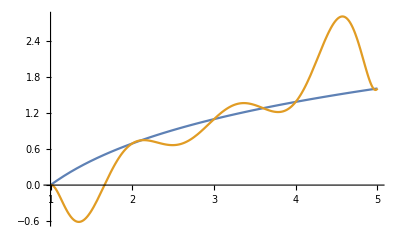

```mathematica
Plot[{Log[x],p[x]},{x,1,5},PlotRange->All]
```

```mathematica
Table[q'[k],{k,1,5}]
d
```

{0.423729,0.847458,1.27119,1.69492,2.11864}

{0.423729,0.847458,1.27119,1.69492,2.11864}

Ejercicio 8:

```mathematica
a=1.47
d=Table[Integrate[x^j,{x,0,j}],{j,0,5}]
```

1.47

{0,1/2,8/3,81/4,1024/5,15625/6}

```mathematica
p[x_]:=Sum[d[[i+1]](x-a)^i/i!,{i,1,Length[d]-1}]
```

Ejercicio 9:

```mathematica
p={0.4,0.5,2.34,3.45,4.567,5.081,5.26}
n=Length[p]-1
```

{0.4,0.5,2.34,3.45,4.567,5.081,5.26}

6

```mathematica
B[i_,x_]:=If[i<n,Which[p[[i]]≤x≤p[[i+1]],(x-p[[i]])/(p[[i+1]]-p[[i]]),p[[i+1]]≤x≤ p[[i+2]],(p[[i+2]]-x)/(p[[i+2]]-p[[i+1]]),True,0],Which[p[[i]]≤x≤ p[[i+1]],(x-p[[i]])/(p[[i+1]]-p[[i]]),True,0]]
```

```mathematica
Table[Plot[B[i,x],{x,p[[1]],p[[n+1]]}],{i,0,n}]
```

```mathematica
nodos=Table[{p[[i]],1-p[[i]]^2/20.78},{i,n+1}]
```

{{0.4,0.9923},{0.5,0.987969},{2.34,0.736497},{3.45,0.427214},{4.567,-0.00372902},{5.081,-0.242375},{5.26,-0.331453}}

```mathematica
f[x_]:=1-x^2/20.78
```

```mathematica
s[x_]:=Sum[f[p[[i+1]]]B[i,x],{i,0,n}]
```

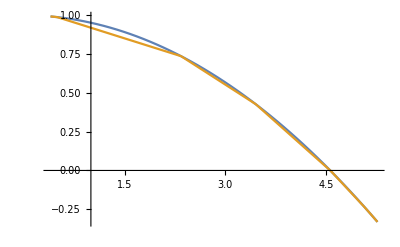

```mathematica
Plot[{f[x],s[x]},{x,p[[1]],p[[n+1]]}]
```

Ejercicio 10:

```mathematica
f[x_]:=Log[1+Abs[x]]
```

```mathematica
a=-2.09;
b=4.56;
n=8;
```

```mathematica
h=(b-a)/n;
nodos=Table[a+i*h,{i,0,n}];
y=Table[f[nodos[[i]]],{i,1,n+1}];
A=2IdentityMatrix[n+1];
For[i=1,i<n,i++,A[[i+1,i+2]]=1/2;A[[i+1,i]]=1/2]
Y=Table[0,{k,n+1}];
For[i=2,i≤n,i++,Y[[i]]=y[[i+1]]-2y[[i]]+y[[i-1]]]
c=LinearSolve[A,3Y/h^2]
```

{0.,-0.527857,0.847763,0.975803,-0.56671,-0.00174026,-0.0891652,-0.0458478,0.}

```mathematica
s[i_,x_]:=Which[nodos[[i]]≤x≤nodos[[i+1]],c[[i]](nodos[[i+1]]-x)^3/(6h)+c[[i+1]](x-nodos[[i]])^3/(6h)+((y[[i+1]]-y[[i]])/h-h/6(c[[i+1]]-c[[i]]))(x-nodos[[i]])+y[[i]]-c[[i]] h^2/6,True,0]
```

```mathematica
S[x_]:=Sum[s[i,x],{i,n}]
```

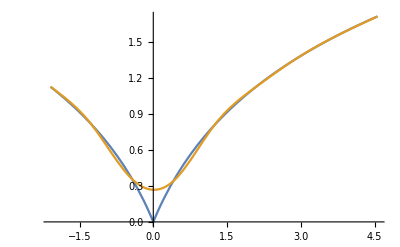

```mathematica
Plot[{f[x],S[x]},{x,nodos[[1]],nodos[[n+1]]}]
```